## F0 basics

We use toric coordinates (X, w) \in C^*. Here R and U are (complex) parameters.

```mathematica
F0 = w+1/w+1/R^2(X+1/X+U)
```

1/w+w+(U+1/X+X)/R^2

Quartic form

```mathematica
Ydef = {Y->-R^2X(w-1/w)};
```

```mathematica
ClearAll[f4];
Y^2/.Ydef/.Solve[F0==0,w]//FullSimplify;
If[!Equal@@%,
Print["Not equal"],Print["Y^2 equal on both solutions."]];First[%];
f4[X_]=%
```

Y^2 equal on both solutions.

(1+X (-2 R^2+U+X)) (1+X (2 R^2+U+X))

Discriminant

```mathematica
ClearAll[delt];
Discriminant[f4[X], X]//FullSimplify
delt[R_,U_] = Simplify[%/256/R^8]
```

256 R^8 (16 R^8+(-4+U^2)^2-8 R^4 (4+U^2))

16 R^8+(-4+U^2)^2-8 R^4 (4+U^2)

Zero discriminant locus

```mathematica
disc0sol = Solve[delt[R,U]==0, U]
```

{{U→-2 (-1+R^2)},{U→2 (-1+R^2)},{U→-2 (1+R^2)},{U→2 (1+R^2)}}

## Weierstrass form

We perform a rational transformation
X --> (a x + b)/(c x + d)
Y --> (a d - b c)/(c x + d)^2 y
and tune a, b, c, d so as to leave the result as a standard Weierstrass cubic

```mathematica
W0 = (c x + d)^4(Y^2-f4[X])/.{X->(a x + b)/(c x + d), Y->(a d - b c)/(c x + d)^2 y}//Simplify
```

-(((d+c x)^2+(b+a x) (b+a x-2 R^2 (d+c x)+U (d+c x))) ((d+c x)^2+(b+a x) (b+a x+2 R^2 (d+c x)+U (d+c x))))+(b c-a d)^2 y^2

Clearly we want a d - b c = 1,  and we take  d = (1+b c)/a

```mathematica
W1 = W0/.{d->(1+b c)/a}//Simplify
```

-1/a^4((1+b c+a c x)^2+a (b+a x) (a b+a^2 x-2 R^2 (1+b c+a c x)+U (1+b c+a c x))) ((1+b c+a c x)^2+a (b+a x) ((1+b c) (2 R^2+U)+a^2 x+a (b+c (2 R^2+U) x)))+y^2

We set up the equations we want to solve for a b c d

```mathematica
Clear[eqns];
eqns = {
Coefficient[W1, x^4]==0,
Coefficient[W1, x^3]==-4,
Coefficient[W1, x^2]==0
}//Simplify
```

{a^4+c^4+2 a^3 c U+2 a c^3 U+a^2 c^2 (2-4 R^4+U^2)==0,2 (2 a^3 b+(2 c^3 (1+b c))/a+c^2 (3+4 b c) U+a^2 (U+4 b c U)+a c (1+2 b c) (2-4 R^4+U^2))==4,6 a^3 b^2+(6 c^2 (1+b c)^2)/a+6 a^2 b (1+2 b c) U+6 c (1+3 b c+2 b^2 c^2) U+a (1+6 b c+6 b^2 c^2) (2-4 R^4+U^2)==0}

```mathematica
Clear[sol];
Solve[eqns, {a,b,c}];
sol = FullSimplify[%, {Im[R]>0, 0<U<1}];
```

```mathematica
(* Very slow *)
(*
W2list = W1/.sol//FullSimplify;
If[!Equal@@W2list,
Print["Not equal"],Print["W2 equal on all solutions for a b c d"]];First[%];
W3 = %
*)
```

```mathematica
(* copied for convenience *)
W3 = 1/216 (4+4 R^4-U^2+12 x) (16 R^8-8 R^4 (5+U^2-3 x)+(-4+U^2-12 x) (-4+U^2+6 x))+y^2;
```

We define cubic f3 in x such that the curve is y^2 = f3(x)

```mathematica
ClearAll[f3];
f3[x_]=Simplify[(-W3/.{y->0})]
```

-1/216 (4+4 R^4-U^2+12 x) (16 R^8-8 R^4 (5+U^2-3 x)+(-4+U^2-12 x) (-4+U^2+6 x))

```mathematica
g2=Simplify[Coefficient[W3, x]]
```

1/12 (16 R^8+(-4+U^2)^2-8 R^4 (2+U^2))

```mathematica
g3=Simplify[W3/.{x->0,y->0}]
```

1/216 (4+4 R^4-U^2) (16 R^8+(-4+U^2)^2-8 R^4 (5+U^2))

```mathematica
(* check *)
(y^2-(4x^3-g2 x-g3))-W3//Simplify
```

0

## Nodal curve parametrization

We want to now parametrize the nodes of the curve with a rational parametrization

```mathematica
rhs0 = f4[X]/.disc0sol//Simplify
```

{(1+X)^2 (1+(2-4 R^2) X+X^2),(-1+X)^2 (1+(-2+4 R^2) X+X^2),(-1+X)^2 (1-2 (1+2 R^2) X+X^2),(1+X)^2 (1+(2+4 R^2) X+X^2)}

For the first branch, we see that X -> 2(1-2R^2-t)/(t^2-1) makes the second factor into a perfect square

```mathematica
First[rhs0]/.{X->2(1-2R^2-t)/(t^2-1)}//Simplify
```

((-4 R^2+(-1+t)^2)^2 (1+(-2+4 R^2) t+t^2)^2)/((-1+t^2)^4)

We therefore propose.

```mathematica
(* initial node parametrization *)
(* Note that we have picked a particular branch Y = Sqrt[Y^2] *)
pXYt = {
{X->2(1-2R^2-t)/(t^2-1), Y->(4 R^2 (-1+t)^3+(-1+t)^4-16 R^4 t)/((-1+t^2)^2)},
{X->-2(1-2R^2-t)/(t^2-1), Y->(4 R^2 (-1+t)^3+(-1+t)^4-16 R^4 t)/((-1+t^2)^2)},
{X->-2(1+2R^2-t)/(t^2-1), Y->(-4 R^2 (-1+t)^3+(-1+t)^4-16 R^4 t)/((-1+t^2)^2)},
{X->2(1+2R^2-t)/(t^2-1), Y->(-4 R^2 (-1+t)^3+(-1+t)^4-16 R^4 t)/((-1+t^2)^2)}
};
```

```mathematica
(* check *)
Simplify@MapThread[#1/.#2&, {Y^2-rhs0, pXYt}]
```

{0,0,0,0}

We would also like the parametrization in the original toric coordinates (X, w)
We do this by changing coordinates (X, Y) --> (X, w) and picking the branch which satisfies the original equation F0 == 0

```mathematica
pXwt=MapThread[
Function[{F0i,xy},
With[{
x=X/. xy,
y=Y/. xy
},
Module[{wBranches, candidates},
wBranches=FullSimplify[w/. Solve[(Y/. Ydef)==Y,w]/.{X->x,Y->y}]//PowerExpand//Simplify;
candidates={X->x,w->#}&/@wBranches;
SelectFirst[candidates,PossibleZeroQ[F0i/. #]&  ]
]
]
],{F0/. disc0sol,pXYt}]
```

{{X→(2 (1-2 R^2-t))/(-1+t^2),w→((-1+t) (-1+2 R^2+t))/(2 R^2 (1+t))},{X→-(2 (1-2 R^2-t))/(-1+t^2),w→-((-1+t) (-1+2 R^2+t))/(2 R^2 (1+t))},{X→-(2 (1+2 R^2-t))/(-1+t^2),w→((1+2 R^2-t) (-1+t))/(2 R^2 (1+t))},{X→(2 (1+2 R^2-t))/(-1+t^2),w→-((1+2 R^2-t) (-1+t))/(2 R^2 (1+t))}}

```mathematica
nodes = First@SolveAlways[#==0, R]&/@rhs0
```

{{X→-1},{X→1},{X→1},{X→-1}}

```mathematica
t12 = Solve[#, t]&/@Thread[(X/.pXwt) == (X/.nodes)]
```

{{{t→1-2 R},{t→1+2 R}},{{t→1-2 R},{t→1+2 R}},{{t→ⅈ (-ⅈ+2 R)},{t→-ⅈ (ⅈ+2 R)}},{{t→ⅈ (-ⅈ+2 R)},{t→-ⅈ (ⅈ+2 R)}}}

Note that the nodes are at finite parameter t. To shift it to 0, \infty, we define a new rational parameter
z = (t - t1)/(t - t2) where t1, t2 correspond to the nodes as above

```mathematica
tToz = First@Solve[z==(t-(t/.#[[1]]))/(t-(t/.#[[2]])), t]&/@t12
```

{{t→(-1+2 R+z+2 R z)/(-1+z)},{t→(-1+2 R+z+2 R z)/(-1+z)},{t→-(ⅈ (-ⅈ+2 R+ⅈ z+2 R z))/(-1+z)},{t→-(ⅈ (-ⅈ+2 R+ⅈ z+2 R z))/(-1+z)}}

We thus find the rational parametrizations we are looking for

```mathematica
pXwz = Simplify@MapThread[#1/.#2&, {pXwt, tToz}]
```

{{X→-((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),w→((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))},{X→((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)),w→-((1+z) (1+R (-1+z)+z))/((-1+z) (-1+R+z+R z))},{X→((-1+z) (R (-1+z)+ⅈ (1+z)))/((1+z) (ⅈ (-1+z)+R (1+z))),w→((1+z) (R (-1+z)+ⅈ (1+z)))/((-1+z) (ⅈ (-1+z)+R (1+z)))},{X→-((-1+z) (R (-1+z)+ⅈ (1+z)))/((1+z) (ⅈ (-1+z)+R (1+z))),w→-((1+z) (R (-1+z)+ⅈ (1+z)))/((-1+z) (ⅈ (-1+z)+R (1+z)))}}

```mathematica
(* check *)
Simplify@MapThread[#1/.#2&, {F0/.disc0sol, pXwz}]
```

{0,0,0,0}

## Kerr Doran period -- Imaginary part

We first define a useful helper function to extract the roots and exponents of rational parametrizations we computed above

```mathematica
ClearAll[RatData];
RatData[expr_,var_]:=Module[{t,num,den,fn,fd,all,linear},(*make sure it's really a single rational expression*)
t=Together[expr];
num=Numerator[t];
den=Denominator[t];
(*factor numerator and denominator in var*)
fn=Rest@FactorList[num];
(*{{factor,exp},...}*)
fd=Rest@FactorList[den];
(*denominator factors get negative exponents*)all=Join[fn,{{#[[1]],-#[[2]]}&/@fd}//Flatten[#,1]&];
(*keep only true linear polynomials in var*)linear=Select[all,PolynomialQ[First[#],var]&&Exponent[First[#],var]==1&];
(*extract exponents and roots*)
{
(*(a) exponents*)
linear[[All,2]],
(*(b) roots:for a z+b==0->z=-b/a*)Simplify[-Coefficient[#[[1]],var,0]/Coefficient[#[[1]],var,1]]&/@linear
}];

(* test *)
expr=-(((-1+z) (1+R (-1+z)+z))/((1+z) (-1+R+z+R z)));
Print["--- Test ---"]
{exponents,roots}=RatData[expr,z];
exponents
roots
ClearAll[expr,exponents,roots]
```

--- Test ---

{1,1,-1,-1}

{1,(-1+R)/(1+R),-1,(1-R)/(1+R)}

Applying the Kerr Doran prescription now for the imaginary part of the period, for the first branch. The other branches do not contribute anything new to the discussion (they are related by R \to \ii R).

```mathematica
{dvec, avec} = RatData[X/.First[pXwz], z]
{evec, bvec} = RatData[w/.First[pXwz], z]
```

{{1,1,-1,-1},{1,(-1+R)/(1+R),-1,(1-R)/(1+R)}}

{{1,1,-1,-1},{-1,(-1+R)/(1+R),1,(1-R)/(1+R)}}

```mathematica
A=1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
```

(BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]-BW[(1+R)/(1-R)]+BW[(1+R)/(-1+R)])/π

We can simplify this further using some identities for the Bloch Wigner function

```mathematica
BWRules = {{BW[z_]:>BW[1-1/z]}, {BW[z_]:>BW[1/(1-z)]}, {BW[z_]:>-BW[1/z]}, {BW[z_]:>-BW[1-z]}, {BW[z_]:>-BW[-z/(1-z)]}};
BWFiveTerm[x_,y_] := BW[x] + BW[y] + BW[(1-x)/(1-x y)] + BW[1-x y] + BW[(1-y)/(1-x y)];
```

```mathematica
Cases[A, BW[__], Infinity]
```

{BW[(1-R)/(1+R)],BW[(-1+R)/(1+R)],BW[(1+R)/(1-R)],BW[(1+R)/(-1+R)]}

```mathematica
BW[(1+R)/(1-R)]/.BWRules//Simplify
```

{BW[(2 R)/(1+R)],BW[(-1+R)/(2 R)],-BW[(1-R)/(1+R)],-BW[(2 R)/(-1+R)],-BW[(1+R)/(2 R)]}

```mathematica
BW[(1+R)/(-1+R)]/.BWRules//Simplify
```

{BW[2/(1+R)],BW[1/2-R/2],-BW[(-1+R)/(1+R)],-BW[-2/(-1+R)],-BW[(1+R)/2]}

```mathematica
rules = {
BW[(1+R)/(1-R)]->-BW[(1-R)/(1+R)],
BW[(1+R)/(-1+R)]->-BW[(-1+R)/(1+R)]
};
A1 = A/.rules//Simplify
```

(2 (BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]))/π

To simplify it further, we note the following instance of the five term relation

```mathematica
BWFiveTerm[R, -1]
```

BW[-1]+BW[R]+BW[2/(1+R)]+BW[(1-R)/(1+R)]+BW[1+R]

```mathematica
BW[2/(1+R)]/.BWRules//Simplify
```

{BW[1/2-R/2],BW[(1+R)/(-1+R)],-BW[(1+R)/2],-BW[(-1+R)/(1+R)],-BW[-2/(-1+R)]}

```mathematica
BW[1+R]/.BWRules//Simplify
```

{BW[R/(1+R)],BW[-1/R],-BW[1/(1+R)],-BW[-R],-BW[1+1/R]}

```mathematica
rules={
BW[2/(1+R)]->-BW[(-1+R)/(1+R)],
BW[-1]->0,
BW[1+R]->-BW[-R]
};
BWFiveTerm[R, -1]/.rules//Simplify
Solve[%==0, BW[(1-R)/(1+R)]]
A2 = A1/.First[%]//Simplify
```

-BW[-R]+BW[R]+BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]

{{BW[(1-R)/(1+R)]→BW[-R]-BW[R]+BW[(-1+R)/(1+R)]}}

(2 (BW[-R]-BW[R]))/π

#### Testing identities and five term relation

```mathematica
BWEval={BW[x_]:>Im[PolyLog[2, x]]+Arg[1-x]Log[Abs[x]]};
rand := RandomComplex[{-1-I, 1+I}];
```

```mathematica
BWFiveTerm[x,y]/.{x->rand, y->rand}/.BWEval
```

5.55112×10^-16

```mathematica
AllTrue[Table[BWFiveTerm[x,y]/.{x->rand, y->rand}/.BWEval, {1000}], Abs[#]<10^-10&]
```

True

```mathematica
Plot3D[ReIm[BWFiveTerm[x, y]/.BWEval], {x, -3, 3}, {y, -3, 3},
PlotRange->{Automatic,Automatic,{-1,1}}
]
```

-Graphics3D-

```mathematica
-BW[-R]+BW[R]+BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]/.{R->R1+I R2}/.BWEval;
Plot3D[Im[%], {R1, -3, 3}, {R2, -3, 3},
PlotRange->{Automatic, Automatic, {-2, 2}}
]
```

-Graphics3D-

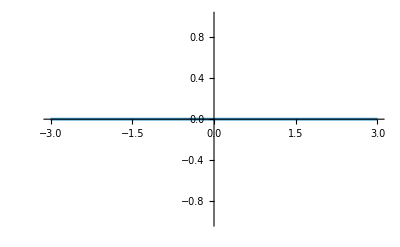

```mathematica
Plot[-BW[-R]+BW[R]+BW[(1-R)/(1+R)]-BW[(-1+R)/(1+R)]/.BWEval, {R, -3, 3}]
```

```mathematica
BW[z]-(BW[z]/.BWRules[[1]])/.{z->z1+I z2}
Plot3D[Re[%/.BWEval], {z1, -3, 3}, {z2, -3, 3}]
```

-BW[1-1/(z1+ⅈ z2)]+BW[z1+ⅈ z2]

-Graphics3D-

## Kerr Doran period -- Full

We are trying to reproduce the quantum volumes in the F0 Dendroscopy paper

```mathematica
QuantumVolume[R_]:=2I/Pi^2 (Li2[-R]-Li2[R]);
```

```mathematica
{dvec, avec} = RatData[X/.First[pXwz], z]
{evec, bvec} = RatData[w/.First[pXwz], z]
{Xat0, wat0} = Simplify@Limit[{X,w}/.First[pXwz], z->0]
{XatInf, watInf} = Simplify@Limit[{X,w}/.First[pXwz], z->Infinity]
```

{{1,1,-1,-1},{1,(-1+R)/(1+R),-1,(1-R)/(1+R)}}

{{1,1,-1,-1},{-1,(-1+R)/(1+R),1,(1-R)/(1+R)}}

{-1,1}

{-1,1}

```mathematica
(* Away from R = 0, 1, "Generic" R: *)
```

```mathematica
b0 = -1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

b1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[XatInf])//Simplify;

b2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

b3 = 1/2/Pi Log[XatInf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = b0 + b1 + b2 + b3//Simplify
```

1/2 (ⅈ (ⅈ π-Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)])+1/π(-2 Li2[(1-R)/(1+R)]+2 Li2[(-1+R)/(1+R)]+2 Li2[(1+R)/(1-R)]-2 Li2[(1+R)/(-1+R)]-ⅈ π Log[1/(1-R)]+ⅈ π Log[R/(-1+R)]-ⅈ π Log[1/(1+R)]+Log[1/(1-R)] Log[(1-R)/(1+R)]-Log[R/(-1+R)] Log[(1-R)/(1+R)]+Log[1/(1+R)] Log[(1-R)/(1+R)]+Log[1/(1-R)] Log[(-1+R)/(1+R)]-Log[R/(-1+R)] Log[(-1+R)/(1+R)]+Log[1/(1+R)] Log[(-1+R)/(1+R)]+ⅈ π Log[R/(1+R)]-Log[(1-R)/(1+R)] Log[R/(1+R)]-Log[(-1+R)/(1+R)] Log[R/(1+R)]))

```mathematica
(* FullSimplify doesn't help much *)
```

```mathematica
B/.{Li2[z_]:>PolyLog[2, z]};
FullSimplify[%, R∈Complexes&&(R!=0)&&(R!=1)]
```

-1/(6 π)(6 ArcTanh[(1+R)/(-1+R)] (-ⅈ π-2 ArcTanh[R]+Log[-1+R]+Log[1/(1+R)])-3 ⅈ π Log[(-1+R)/(1+R)]-6 π √(-1/(1+R)^2) Log[(-1+R)/(1+R)]-6 π R √(-1/(1+R)^2) Log[(-1+R)/(1+R)]+3 Log[(-1+R)/(1+R)]^2+π (π+3 ⅈ Log[-1+2/(1+R)])+6 ArcTanh[(-1+R)/(1+R)] (-ⅈ π+Log[(-1+R)/(1+R)]+Log[-1+2/(1+R)])-6 PolyLog[2,(1+R)/(1-R)]+12 PolyLog[2,(1+R)/(-1+R)]+6 PolyLog[2,-1+2/(1+R)])

```mathematica
(* Assuming Im[R]>0 helps *)
B1 = FullSimplify[B, Im[R]>0]
```

1/π(Li2[(-1+R)/(1+R)]+Li2[(1+R)/(1-R)]-Li2[(1+R)/(-1+R)]-Li2[-1+2/(1+R)]+ⅈ Log[-1+R] (π+2 ⅈ Log[R])+2 ⅈ π Log[R]+(-ⅈ π+2 Log[R]) Log[1+R])

We use Li2 identities and a tentative five term relation in terms of the Roger’s L function

```mathematica
Li2Rules = {{Li2[z_]:>-Li2[1/z]-Pi^2/6-1/2 Log[-1/z]^2}, {Li2[z_]:>-Li2[1-z]+Pi^2/6-Log[z]Log[1-z]}};
```

```mathematica
Li2FiveTerm[x_, y_] = Simplify[L[x]+L[y]+L[1-x y]+L[(1-x)/(1-x y)]+L[(1-y)/(1-x y)]-3Pi^2/6/.{L[z_]:>Li2[z]+1/2Log[z]Log[1-z]}];
```

```mathematica
Cases[Expand[B], Li2[__], Infinity]
```

{Li2[(1-R)/(1+R)],Li2[(-1+R)/(1+R)],Li2[(1+R)/(1-R)],Li2[(1+R)/(-1+R)]}

```mathematica
Li2[(1+R)/(1-R)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2),1/6 (π^2-6 Li2[(2 R)/(-1+R)]-6 Log[(2 R)/(-1+R)] Log[(1+R)/(1-R)])}

```mathematica
Li2[(1+R)/(-1+R)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[(1-R)/(1+R)]^2),1/6 (π^2-6 Li2[-2/(-1+R)]-6 Log[-2/(-1+R)] Log[(1+R)/(-1+R)])}

```mathematica
rules={
Li2[(1+R)/(1-R)]->1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2),
Li2[(1+R)/(-1+R)]->1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[-(-1+R)/(1+R)]^2)
};
B2 = FullSimplify[B1/.rules, Im[R]>0]
```

1/(2 π)(4 Li2[(-1+R)/(1+R)]-4 Li2[-1+2/(1+R)]+2 ⅈ Log[-1+R] (π+2 ⅈ Log[R])+4 ⅈ π Log[R]-Log[(-1+R)/(1+R)]^2+2 (-ⅈ π+2 Log[R]) Log[1+R]+Log[-1+2/(1+R)]^2)

```mathematica
Cases[Expand[B1], Li2[__], Infinity]
```

{Li2[(1-R)/(1+R)],Li2[(-1+R)/(1+R)]}

```mathematica
NewFiveTerm[R]
```

Li2[R]+1/2 (-π^2+2 Li2[-1]+2 Li2[2/(1+R)]+2 Li2[1+R]+2 Li2[-1+2/(1+R)]+ⅈ π Log[2]+(-ⅈ π+Log[-1+R]) Log[R]+Log[2/(1+R)] Log[(-1+R)/(1+R)]+(-3 ⅈ π+Log[R]) Log[1+R]+Log[(2 R)/(1+R)] Log[-1+2/(1+R)])

```mathematica
Li2[2/(1+R)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(1+R)/2]-3 Log[1/2 (-1-R)]^2),1/6 (π^2-6 Li2[(-1+R)/(1+R)]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)])}

```mathematica
Li2[1+R]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[1/(1+R)]-3 Log[-1/(1+R)]^2),1/6 (π^2-6 Li2[-R]-6 Log[-R] Log[1+R])}

```mathematica
Li2[-1]/.Li2Rules//Simplify
```

{-π^2/6-Li2[-1],1/6 (π^2-6 Li2[2]-6 ⅈ π Log[2])}

```mathematica
rules={
Li2[2/(1+R)]->1/6 (π^2-6 Li2[(-1+R)/(1+R)]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)]),
Li2[1+R]->1/6 (π^2-6 Li2[-R]-6 Log[-R] Log[1+R]),
Li2[-1]->-Pi^2/12
};
FullSimplify[NewFiveTerm[R]/.rules, Im[R]>0]
Solve[%==0,Li2[-1+2/(1+R)]]
B3 = FullSimplify[B2/.First[%], Im[R]>0]
(*B2 = B1/.First[%]//Simplify*)
```

1/4 (-4 Li2[-R]+4 Li2[R]-4 Li2[(-1+R)/(1+R)]+4 Li2[-1+2/(1+R)]-2 Log[2/(1+R)] Log[(-1+R)/(1+R)]+2 Log[R] (-ⅈ π+Log[-1+R]-Log[1+R])-π (π-2 ⅈ Log[2]+2 ⅈ Log[1+R])+2 Log[(2 R)/(1+R)] Log[-1+2/(1+R)])

{{Li2[-1+2/(1+R)]→1/4 (π^2+4 Li2[-R]-4 Li2[R]+4 Li2[(-1+R)/(1+R)]-2 Log[-1+R] Log[R]+2 Log[2/(1+R)] Log[(-1+R)/(1+R)]+2 Log[R] Log[1+R]-2 ⅈ (π Log[2]-π Log[R]-π Log[1+R])-2 Log[(2 R)/(1+R)] Log[-1+2/(1+R)])}}

-(π^2+2 Li2[-R]-2 Li2[R])/π

#### Testing identities and five term

```mathematica
Li2Eval = {Li2[z_]:>PolyLog[2, z]};
```

```mathematica
Li2[z]-(Li2[z]/.Li2Rules[[1]])
Plot3D[Evaluate[Re[%]/.{z->z1+I z2}/.Li2Eval], {z1,-2,2},{z2,-2,2},
PlotRange->{Automatic, Automatic, {-1,1}}
]
```

π^2/6+Li2[1/z]+Li2[z]+1/2 Log[-1/z]^2

-Graphics3D-

π^2/6+Li2[1/z]+Li2[z]+1/2 Log[-1/z]^2

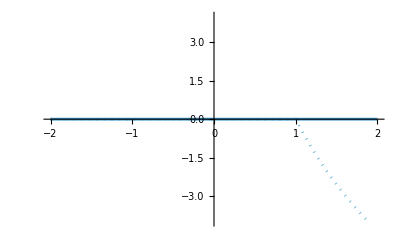

```mathematica
Li2[z]-(Li2[z]/.Li2Rules[[1]])
ReImPlot[%/.Li2Eval, {z, -2, 2},
PlotRange->{Automatic, {-4, 4}}
]
```

```mathematica
Li2[z]-(Li2[z]/.Li2Rules[[2]])
Plot3D[Re[%/.{z->z1+I z2}/.Li2Eval], {z1,-3,3},{z2,-3,3}]
```

-π^2/6+Li2[1-z]+Li2[z]+Log[1-z] Log[z]

-Graphics3D-

-π^2/6+Li2[1-z]+Li2[z]+Log[1-z] Log[z]

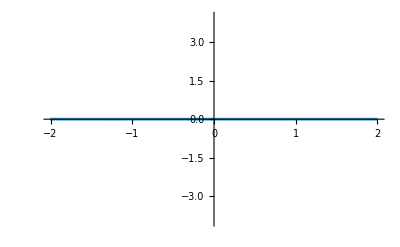

```mathematica
Li2[z]-(Li2[z]/.Li2Rules[[2]])
ReImPlot[%/.Li2Eval, {z, -2, 2},
PlotRange->{Automatic, {-4, 4}}
]
```

```mathematica
With[{z=1.3}, {PolyLog[2, 1/z], -PolyLog[2, z]-Pi^2/6-1/2Log[-z]^2}]
```

{1.01456,1.01456+0. ⅈ}

```mathematica
Li2FiveTerm[rand, rand]/.Li2Eval
```

-2.4701+0.53192 ⅈ

```mathematica
Plot3D[Im[Li2FiveTerm[x, y]/.Li2Eval], {x, -3, 3}, {y, -3, 3},
PlotRange->{Automatic, Automatic, {-50,50}}
]
```

-Graphics3D-

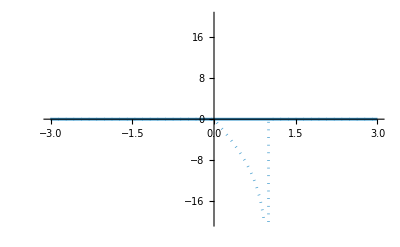

```mathematica
ReImPlot[Li2[(1+R)/(1-R)]-1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2)/.Li2Eval, {R, -3, 3},
PlotRange->{Automatic, {-20, 20}}
]
```

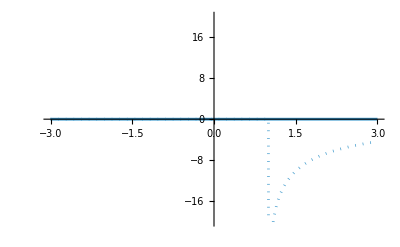

```mathematica
ReImPlot[Li2[(1+R)/(-1+R)]-1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[-(-1+R)/(1+R)]^2)/.Li2Eval, {R, -3, 3},
PlotRange->{Automatic, {-20, 20}}
]
```

Derivative checks

```mathematica
FullSimplify[R D[Li2FiveTerm[R, -1], R], Im[R]>0]
FullSimplify[R D[%/.{Li2'[z_]:>-Log[1-z]/z}, R], Im[R]>0]
```

(-ⅈ π (-1+R^2)+R Log[4]+(-1+R) Log[-1+R]+R (1+R) Log[R]+(-3+R) R Log[1+R])/(-1+R^2)+R (Li2'[R]+Li2'[1+R]-(2 (Li2'[2/(1+R)]+Li2'[-1+2/(1+R)]))/(1+R)^2)

(ⅈ π R)/(1+R)^2

```mathematica
Integrate[1/R(ⅈ π R)/(1+R)^2,R, GeneratedParameters->C]
Integrate[1/R%,R, GeneratedParameters->C]
```

-(ⅈ π)/(1+R)+C[1]

C[2]+(-ⅈ π+C[1]) Log[R]+ⅈ π Log[1+R]

```mathematica
newFT[R_]=FullSimplify[Li2FiveTerm[R,-1]-(C[2]+(-ⅈ π+C[1]) Log[R]+ⅈ π Log[1+R]), Im[R]>0]
```

Li2[R]+1/2 (-π^2-2 C[2]+2 Li2[-1]+2 Li2[2/(1+R)]+2 Li2[1+R]+2 Li2[-1+2/(1+R)]+Log[2/(1+R)] Log[(-1+R)/(1+R)]+ⅈ π (Log[2]+Log[R]-3 Log[1+R])+Log[R] (-2 C[1]+Log[-1+R]+Log[1+R])+Log[(2 R)/(1+R)] Log[-1+2/(1+R)])

```mathematica
{newFT[.3+.4I], newFT[.6+.2I]}/.Li2Eval//Simplify//Chop
Solve[Thread[%=={0,0}], {C[1],C[2]}]//Chop
```

{(-2.91318-2.17759 ⅈ)+(0.693147-0.927295 ⅈ) C[1]-1. C[2],(-1.01081-1.43931 ⅈ)+(0.458145-0.321751 ⅈ) C[1]-1. C[2]}

{{C[1]→0.+3.14159 ⅈ,C[2]→0}}

```mathematica
newFTConst = {C[1]->Pi I, C[2]->0};
```

```mathematica
NewFiveTerm[R_]=FullSimplify[newFT[R]/.newFTConst, Im[R]>0]
```

Li2[R]+1/2 (-π^2+2 Li2[-1]+2 Li2[2/(1+R)]+2 Li2[1+R]+2 Li2[-1+2/(1+R)]+ⅈ π Log[2]+(-ⅈ π+Log[-1+R]) Log[R]+Log[2/(1+R)] Log[(-1+R)/(1+R)]+(-3 ⅈ π+Log[R]) Log[1+R]+Log[(2 R)/(1+R)] Log[-1+2/(1+R)])

```mathematica
Plot3D[Evaluate[ReIm[NewFiveTerm[R1+I R2]/.Li2Eval]], {R1,-3,3},{R2,-3,3}]
```

-Graphics3D-

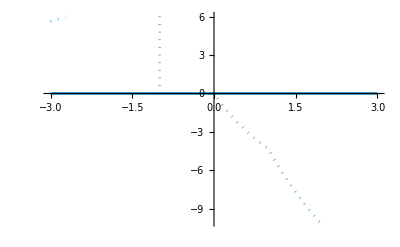

```mathematica
ReImPlot[NewFiveTerm[R]/.Li2Eval, {R,-3,3}]
```

```mathematica
FullSimplify[R D[B, R], Im[R]>0]
FullSimplify[R D[%/.{Li2'[z_]:>-Log[1-z]/z}, R], Im[R]>0]
```

1/(π (-1+R^2)^2)2 ((-1+R^2) (ⅈ π (-1+R+R^2)-(-1+R^2) Log[-1+R]-2 R Log[R]+(-1+R^2) Log[1+R])+(-1+R)^2 R Li2'[(-1+R)/(1+R)]+R (1+R)^2 (Li2'[(1+R)/(1-R)]+Li2'[(1+R)/(-1+R)])+(-1+R)^2 R Li2'[-1+2/(1+R)])

(4 R)/(π-π R^2)

```mathematica
FullSimplify[R D[QuantumVolume[R], R], Im[R]>0]
FullSimplify[R D[%/.{Li2'[z_]:>-Log[1-z]/z}, R], Im[R]>0]
```

-(2 ⅈ R (Li2'[-R]+Li2'[R]))/π^2

(4 ⅈ R)/(π^2 (-1+R^2))

```mathematica
FullSimplify[R D[B3, R], Im[R]>0]
FullSimplify[R D[%/.{Li2'[z_]:>-Log[1-z]/z}, R], Im[R]>0]
```

(2 R (Li2'[-R]+Li2'[R]))/π

(4 R)/(π-π R^2)

#### Zagier’s Li2 five term relation is wrong

```mathematica
ZagierFiveTerm[x_, y_] := Li2[x]+Li2[y]+Li2[(1-x)/(1-x y)]+Li2[1-x y]+Li2[(1-y)/(1-x y)];
```

```mathematica
ZagierFiveTerm[rand, rand]/.Li2Eval
```

3.45033-1.61966 ⅈ

```mathematica
Plot3D[Re[ZagierFiveTerm[x, y]/.Li2Eval], {x, -3, 3}, {y, -3, 3}]
```

-Graphics3D-

## Kerr Doran R = 1, U = 0

```mathematica
delt[1, U]//Simplify
```

U^2 (-16+U^2)

```mathematica
F0/.{R->1,U->0}//Simplify
```

1/w+w+1/X+X

```mathematica
F0/.{R->1,U->4}//FullSimplify
```

4+1/w+w+1/X+X

```mathematica
F0/.{R->1}//FullSimplify
```

U+1/w+w+1/X+X

```mathematica
f4[X]/.{R->1}/.{U->0}//Simplify
Y^2-%/.{X->t^2,Y->t^4-1}//Simplify
```

(-1+X^2)^2

0

```mathematica
Ydef/.
```

```mathematica
w/.Solve[(Y/.Ydef)==Y,w]/.{R->1}//FullSimplify
%/.{X->t^2,Y->t^4-1}//FullSimplify//PowerExpand//Simplify
```

{(-Y+√(4 X^2+Y^2))/(2 X),-(Y+√(4 X^2+Y^2))/(2 X)}

{1/t^2,-t^2}

```mathematica
F0/.{R->1,U->0}/.{X->t^2, w->-t^2}//Simplify
```

0

```mathematica
sol = {X,w}/.{X->t^2, w->-t^2}/.First@Solve[z==(t-1)/(t+1), t]//FullSimplify
F0/.{R->1,U->0}/.Thread[{X,w}->%]//Simplify
```

{(1+z)^2/(-1+z)^2,-(1+z)^2/(-1+z)^2}

0

```mathematica
Solve[(1+X (-2+U+X)) (1+X (2+U+X))==0, X]/.{U->0}
```

{{X→1},{X→1},{X→-1},{X→-1}}

```mathematica
{dvec, avec} = RatData[sol[[1]], z]
{evec, bvec} = RatData[sol[[2]], z]
{Xat0, wat0} = Simplify@Limit[sol, z->0]
{XatInf, watInf} = Simplify@Limit[sol, z->Infinity]
```

{{2,-2},{-1,1}}

{{2,-2},{-1,1}}

{1,-1}

{1,-1}

```mathematica
b0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

b1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[XatInf])//Simplify;

b2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

b3 = 1/2/Pi Log[XatInf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = b0 + b1 + b2 + b3//Simplify
```

π+(4 Li2[-1])/π

```mathematica
B/.{Li2[-1]->-π^2/12}
```

(2 π)/3

```mathematica
A=1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
```

-(4 BW[-1])/π

```mathematica
sol2 = {X,w}/.{X->t^2, w->-t^2}/.First@Solve[z==(t-I)/(t+I), t]//FullSimplify
F0/.{R->1,U->0}/.Thread[{X,w}->%]//Simplify
```

{-(1+z)^2/(-1+z)^2,(1+z)^2/(-1+z)^2}

0

```mathematica
{dvec, avec} = RatData[sol2[[1]], z]
{evec, bvec} = RatData[sol2[[2]], z]
{Xat0, wat0} = Simplify@Limit[sol2, z->0]
{XatInf, watInf} = Simplify@Limit[sol2, z->Infinity]
```

{{2,-2},{-1,1}}

{{2,-2},{-1,1}}

{-1,1}

{-1,1}

```mathematica
b0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

b1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[XatInf])//Simplify;

b2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

b3 = 1/2/Pi Log[XatInf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = b0 + b1 + b2 + b3//Simplify
```

-π+(4 Li2[-1])/π

```mathematica
(8 Li2[-1])/π/.{Li2[-1]->-Pi^2/12}
```

-(2 π)/3

## Kerr Doran R = 1, U = +-4

```mathematica
delt[1, U]/.{U->{4,-4}}//Simplify
```

{0,0}

```mathematica
f4[X]/.{R->1}/.{U->4}//Simplify
Y^2-%/.{X->(t^2-6t+8)/2/t, Y->((8+(-4+t) t) (-8+t^2))/(4 t^2)}//FullSimplify
```

(1+X)^2 (1+X (6+X))

0

```mathematica
t/.Solve[(t^2-6t+8)/2/t==-1, t]
Solve[z==(t-%[[1]])/(t-%[[2]]), t]//Simplify
p = {X->(t^2-6t+8)/2/t, Y->((8+(-4+t) t) (-8+t^2))/(4 t^2)}/.First[%]//FullSimplify
```

{2-2 ⅈ,2+2 ⅈ}

{{t→((2+2 ⅈ) (ⅈ+z))/(-1+z)}}

{X→-1+(2 ⅈ)/(-1+z)-2/(ⅈ+z),Y→-((4+4 ⅈ) z (ⅈ+z^2))/((-1+z)^2 (ⅈ+z)^2)}

```mathematica
Solve[Y-(Y/.Ydef/.{R->1})==0, w]/.p//FullSimplify//PowerExpand//Simplify
F0/.{R->1,U->4}/.p/.%//Simplify
```

{{w→((-1+z) (-ⅈ+z))/((ⅈ+z) (1+z))},{w→-((ⅈ+z) (1+z))/((-1+z) (-ⅈ+z))}}

{(4 (-1+4 ⅈ z^2+z^4))/(-1+z^4),0}

```mathematica
p1 = {X->-1+(2 ⅈ)/(-1+z)-2/(ⅈ+z), w->-((ⅈ+z) (1+z))/((-1+z) (-ⅈ+z))};
```

```mathematica
p1
```

{X→-1+(2 ⅈ)/(-1+z)-2/(ⅈ+z),w→-((ⅈ+z) (1+z))/((-1+z) (-ⅈ+z))}

```mathematica
{dvec, avec} = RatData[X/.p1, z]
{evec, bvec} = RatData[w/.p1, z]
{Xat0, wat0} = Simplify@Limit[{X,w}/.p1, z->0]
{XatInf, watInf} = Simplify@Limit[{X,w}/.p1, z->Infinity]
```

{{1,1,-1,-1},{ⅈ,-1,1,-ⅈ}}

{{1,1,-1,-1},{-ⅈ,-1,1,ⅈ}}

{-1,-1}

{-1,-1}

```mathematica
b0 = -1/2/Pi Sum[If[avec[[j]]==bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

b1 = 1/2/Pi Log[wat0](Log[Xat0]-Log[XatInf])//Simplify;

b2 = -1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

b3 = 1/2/Pi Log[XatInf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = b0 + b1 + b2 + b3//Simplify
```

π-(2 (Li2[-ⅈ]-Li2[ⅈ]))/π

```mathematica
B/.{Li2[z_]:>PolyLog[2,z]}
```

(4 ⅈ Catalan)/π+π

```mathematica
A=1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
A/.BWEval
```

(2 (BW[-ⅈ]-BW[ⅈ]))/π

-(4 Catalan)/π